# Conservation of angular momentum in NV-centers

Tests whether the NV-center Hamiltonian

[Insert equation]

conserves angular momentum.

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Initialisation

## NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
B0 =0*10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)
Axyhf = -2.1*10^6;
Azhf = -2.16*10^6 ; (* Hyperfine interaction [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

## Operators

```mathematica
(* Triplet spin operators *)

Sx = 1/Sqrt[2]{ {  0, 1, 0} , { 1, 0, 1}, {0, 1, 0 } };
Sy = 1/(Sqrt[2] I){ {  0, -1, 0} , { 1, 0, 1}, {0, -1, 0 } };
Sz = { {1, 0, 0 }, {0, 0, 0}, {0, 0, -1}};
eye = IdentityMatrix[3];

(* Electron triplet operators *)

eSx = KroneckerProduct[Sx, eye];
eSy = KroneckerProduct[Sy, eye];
eSz = KroneckerProduct[Sz, eye];

(* Nuclear operators *)

Ix = KroneckerProduct[eye, Sx];
Iy = KroneckerProduct[eye, Sy];
Iz = KroneckerProduct[eye, Sz];

Jz = eSx + Iz;
```

## Hamiltonian

Hhf is the hyperfine interaction.
Hnv is the Hamiltonian of the NV-centre.
Hc is the time-dependent perturbation on the Hamiltonian.
H is the complete Hamiltonian.

```mathematica
Hhf= ( Axyhf( eSx.Ix + eSy.Iy ) + Azhf eSz . Iz); 
Hnv =  ( Dzfs eSz.eSz  + ωs eSz + Pzfs  Iz.Iz - ωI Iz) + Hhf;
Hcop = pulseAmplitude  KroneckerProduct[Sx, Sx]; 
Hc[t_]:= Hcop Sin[ 2π pulseFreq t + pulsePhase ]  ;
H[t_] := Hnv+ Hc[t]

systemSize = Length[H[0]];
```

## Density matrix

```mathematica
density = Table[ ρ[i, j][t],{i, 1, systemSize}, {j, 1, systemSize}] ;
Do[
density[[j, i]] = Conjugate[density[[i,j]]];
, {i, 1, systemSize}, {j, i+1, systemSize}];

density // MatrixForm
```

(ρ[1,1][t] | ρ[1,2][t] | ρ[1,3][t] | ρ[1,4][t] | ρ[1,5][t] | ρ[1,6][t] | ρ[1,7][t] | ρ[1,8][t] | ρ[1,9][t]
Conjugate[ρ[1,2][t]] | ρ[2,2][t] | ρ[2,3][t] | ρ[2,4][t] | ρ[2,5][t] | ρ[2,6][t] | ρ[2,7][t] | ρ[2,8][t] | ρ[2,9][t]
Conjugate[ρ[1,3][t]] | Conjugate[ρ[2,3][t]] | ρ[3,3][t] | ρ[3,4][t] | ρ[3,5][t] | ρ[3,6][t] | ρ[3,7][t] | ρ[3,8][t] | ρ[3,9][t]
Conjugate[ρ[1,4][t]] | Conjugate[ρ[2,4][t]] | Conjugate[ρ[3,4][t]] | ρ[4,4][t] | ρ[4,5][t] | ρ[4,6][t] | ρ[4,7][t] | ρ[4,8][t] | ρ[4,9][t]
Conjugate[ρ[1,5][t]] | Conjugate[ρ[2,5][t]] | Conjugate[ρ[3,5][t]] | Conjugate[ρ[4,5][t]] | ρ[5,5][t] | ρ[5,6][t] | ρ[5,7][t] | ρ[5,8][t] | ρ[5,9][t]
Conjugate[ρ[1,6][t]] | Conjugate[ρ[2,6][t]] | Conjugate[ρ[3,6][t]] | Conjugate[ρ[4,6][t]] | Conjugate[ρ[5,6][t]] | ρ[6,6][t] | ρ[6,7][t] | ρ[6,8][t] | ρ[6,9][t]
Conjugate[ρ[1,7][t]] | Conjugate[ρ[2,7][t]] | Conjugate[ρ[3,7][t]] | Conjugate[ρ[4,7][t]] | Conjugate[ρ[5,7][t]] | Conjugate[ρ[6,7][t]] | ρ[7,7][t] | ρ[7,8][t] | ρ[7,9][t]
Conjugate[ρ[1,8][t]] | Conjugate[ρ[2,8][t]] | Conjugate[ρ[3,8][t]] | Conjugate[ρ[4,8][t]] | Conjugate[ρ[5,8][t]] | Conjugate[ρ[6,8][t]] | Conjugate[ρ[7,8][t]] | ρ[8,8][t] | ρ[8,9][t]
Conjugate[ρ[1,9][t]] | Conjugate[ρ[2,9][t]] | Conjugate[ρ[3,9][t]] | Conjugate[ρ[4,9][t]] | Conjugate[ρ[5,9][t]] | Conjugate[ρ[6,9][t]] | Conjugate[ρ[7,9][t]] | Conjugate[ρ[8,9][t]] | ρ[9,9][t])

### Dephasing

```mathematica
dephasingConstants = Table[ Γ[i, j], {i, 1, Length[density]}, {j, 1, Length[density]}];
dephasing = Table[
If[ i ≠ j, dephasingConstants[[i, j]] density[[i, j]], 0]
,  {i, 1, Length[density]}, {j, 1, Length[density]}];
Do [
Γ[i, j] = -10^6;
, {i, 1, Length[density]}, {j, 1, Length[density]}];

dephasing // MatrixForm
```

(0 | -1000000 ρ[1,2][t] | -1000000 ρ[1,3][t] | -1000000 ρ[1,4][t] | -1000000 ρ[1,5][t] | -1000000 ρ[1,6][t] | -1000000 ρ[1,7][t] | -1000000 ρ[1,8][t] | -1000000 ρ[1,9][t]
-1000000 Conjugate[ρ[1,2][t]] | 0 | -1000000 ρ[2,3][t] | -1000000 ρ[2,4][t] | -1000000 ρ[2,5][t] | -1000000 ρ[2,6][t] | -1000000 ρ[2,7][t] | -1000000 ρ[2,8][t] | -1000000 ρ[2,9][t]
-1000000 Conjugate[ρ[1,3][t]] | -1000000 Conjugate[ρ[2,3][t]] | 0 | -1000000 ρ[3,4][t] | -1000000 ρ[3,5][t] | -1000000 ρ[3,6][t] | -1000000 ρ[3,7][t] | -1000000 ρ[3,8][t] | -1000000 ρ[3,9][t]
-1000000 Conjugate[ρ[1,4][t]] | -1000000 Conjugate[ρ[2,4][t]] | -1000000 Conjugate[ρ[3,4][t]] | 0 | -1000000 ρ[4,5][t] | -1000000 ρ[4,6][t] | -1000000 ρ[4,7][t] | -1000000 ρ[4,8][t] | -1000000 ρ[4,9][t]
-1000000 Conjugate[ρ[1,5][t]] | -1000000 Conjugate[ρ[2,5][t]] | -1000000 Conjugate[ρ[3,5][t]] | -1000000 Conjugate[ρ[4,5][t]] | 0 | -1000000 ρ[5,6][t] | -1000000 ρ[5,7][t] | -1000000 ρ[5,8][t] | -1000000 ρ[5,9][t]
-1000000 Conjugate[ρ[1,6][t]] | -1000000 Conjugate[ρ[2,6][t]] | -1000000 Conjugate[ρ[3,6][t]] | -1000000 Conjugate[ρ[4,6][t]] | -1000000 Conjugate[ρ[5,6][t]] | 0 | -1000000 ρ[6,7][t] | -1000000 ρ[6,8][t] | -1000000 ρ[6,9][t]
-1000000 Conjugate[ρ[1,7][t]] | -1000000 Conjugate[ρ[2,7][t]] | -1000000 Conjugate[ρ[3,7][t]] | -1000000 Conjugate[ρ[4,7][t]] | -1000000 Conjugate[ρ[5,7][t]] | -1000000 Conjugate[ρ[6,7][t]] | 0 | -1000000 ρ[7,8][t] | -1000000 ρ[7,9][t]
-1000000 Conjugate[ρ[1,8][t]] | -1000000 Conjugate[ρ[2,8][t]] | -1000000 Conjugate[ρ[3,8][t]] | -1000000 Conjugate[ρ[4,8][t]] | -1000000 Conjugate[ρ[5,8][t]] | -1000000 Conjugate[ρ[6,8][t]] | -1000000 Conjugate[ρ[7,8][t]] | 0 | -1000000 ρ[8,9][t]
-1000000 Conjugate[ρ[1,9][t]] | -1000000 Conjugate[ρ[2,9][t]] | -1000000 Conjugate[ρ[3,9][t]] | -1000000 Conjugate[ρ[4,9][t]] | -1000000 Conjugate[ρ[5,9][t]] | -1000000 Conjugate[ρ[6,9][t]] | -1000000 Conjugate[ρ[7,9][t]] | -1000000 Conjugate[ρ[8,9][t]] | 0)

## Functions

For a density matrix ρ in the space A_1 ⊗ A_2 ⊗ ... ⊗ A_n, the function will return the reduced density matrix ρ_A_1.

```mathematica
GetSubsystemA[density_, subSystemSize_] := Map[ Tr, Partition[ density, {Length[density]/subSystemSize, Length[density]/subSystemSize}], {2}];
```

## Simulation parameters

```mathematica
pulseAmplitude = 7*10^6; (* [Hz] *)
pulsePhase = 0; (* [Rad] *)
pulseFreq = Dzfs - Pzfs;

tStart = 0; (* [s] *)
tEnd = 5*10^-6; (* [s] *)
tStep = (tEnd - tStart) / 100;  (* [s] *)
calculations = Table[t, {t, tStart, tEnd, tStep}] // Length ;
```

## Define basis-states

```mathematica
electronTripletBasis[1] = {1, 0, 0};
electronTripletBasis[0] = {0, 1, 0};
electronTripletBasis[-1] = {0, 0, 1};

nuclearBasis[1] = {1, 0, 0};
nuclearBasis[0] = {0, 1, 0};
nuclearBasis[-1] = {0, 0, 1};

getBasisState[s_, i_] := KroneckerProduct[ electronTripletBasis[s], nuclearBasis[i] ] // Flatten;

getBasisStatesWithAngularMomentum[j_] := Module[
{combinations =Flatten[Outer[ {#1 + #2, #1, #2} &, {1, 0, -1}, {1, 0, -1}], 1]},
Table[ KroneckerProduct[ electronTripletBasis[ e[[2]] ], nuclearBasis[ e[[3]] ] ] // Flatten, {e, Select[combinations, #[[1]] == j &]}]
];
```

## Define initial state of the system

```mathematica
initialAngularMomentum = 0;
initialState = KroneckerProduct[electronTripletBasis[0], nuclearBasis[0]] // Flatten;

initialStates = {
getBasisState[0,1]  ,
getBasisState[1,-1] ,
1/Sqrt[2](getBasisState[0,0] + getBasisState[0,1])
};

initialAngularMomenta = Table[ v. Jz . v, {v, initialStates}];
initialDensityMatrices = Table [ Outer[Times, v, Conjugate[v] ],  {v, initialStates}  ];
```

## Master equation

```mathematica
eqnTotal = ⅈ  D[ density, t] - (H[t].density - density.H[t]) - dephasing // Simplify;
eqns = Table[ eqnTotal[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
diffeqs = Table[ eqns[[i]] == 0, {i, 1, Length[eqns]}];
funcs =Table[ density[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
```

## Perform simulation

Initial angular momentum: 1

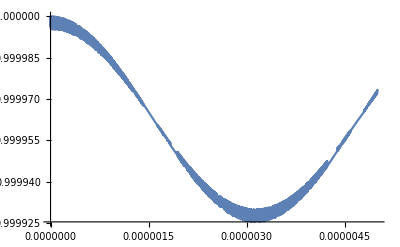

Initial angular momentum: -1

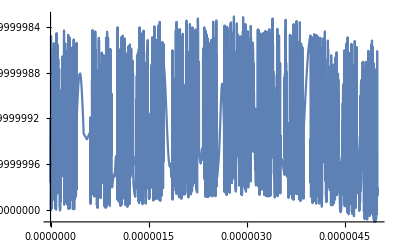

Initial angular momentum: 1/2

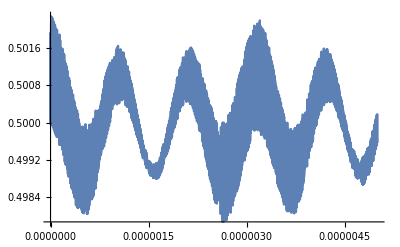

```mathematica
For[i=1,i≤Length[initialStates],i++,

density0 = initialDensityMatrices[[i]];
initialStateEqs =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten;
params = { diffeqs, initialStateEqs } // Flatten;

sol = NDSolve[ params /. f -> pulseFreq, funcs, {t, tStart, tEnd}, 
PrecisionGoal->10,AccuracyGoal->10, MaxSteps->Infinity];

densitySol = density /. sol[[1]];

Print[ "Initial angular momentum: ",  initialAngularMomenta[[i]]] ;

Print[Plot[ Tr[ Jz . densitySol], {t, tStart, tEnd}  ]];
 ]
```

## Evolution of pure states

```mathematica
puresStateAngularMomenta = {
-2,
-1,
-1,
0,
0,
1,
1,
2
};

pureStates = {
getBasisState[-1, -1],
getBasisState[-1,0],
getBasisState[0, -1],
getBasisState[1, -1],
getBasisState[0, 0],
getBasisState[1, 0],
getBasisState[0, 1],
getBasisState[1,1]
};

pureStateDensityMatrices = Table [ Outer[Times, v, Conjugate[v] ],  {v, pureStates}  ];
```

```mathematica
density0 = pureStateDensityMatrices[[1]];
pureStates =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten
```

{ρ[1,1][0]==0,ρ[1,2][0]==0,ρ[1,3][0]==0,ρ[1,4][0]==0,ρ[1,5][0]==0,ρ[1,6][0]==0,ρ[1,7][0]==0,ρ[1,8][0]==0,ρ[1,9][0]==0,ρ[2,2][0]==0,ρ[2,3][0]==0,ρ[2,4][0]==0,ρ[2,5][0]==0,ρ[2,6][0]==0,ρ[2,7][0]==0,ρ[2,8][0]==0,ρ[2,9][0]==0,ρ[3,3][0]==0,ρ[3,4][0]==0,ρ[3,5][0]==0,ρ[3,6][0]==0,ρ[3,7][0]==0,ρ[3,8][0]==0,ρ[3,9][0]==0,ρ[4,4][0]==0,ρ[4,5][0]==0,ρ[4,6][0]==0,ρ[4,7][0]==0,ρ[4,8][0]==0,ρ[4,9][0]==0,ρ[5,5][0]==0,ρ[5,6][0]==0,ρ[5,7][0]==0,ρ[5,8][0]==0,ρ[5,9][0]==0,ρ[6,6][0]==0,ρ[6,7][0]==0,ρ[6,8][0]==0,ρ[6,9][0]==0,ρ[7,7][0]==0,ρ[7,8][0]==0,ρ[7,9][0]==0,ρ[8,8][0]==0,ρ[8,9][0]==0,ρ[9,9][0]==1}

Initial angular momentum: -2

Average probability: 1.

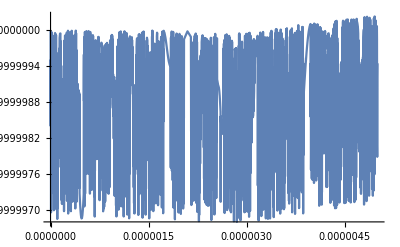

Initial angular momentum: -1

Average probability: 0.999954

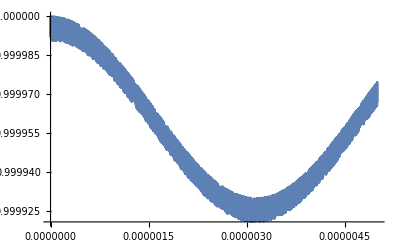

Initial angular momentum: -1

Average probability: 0.999954

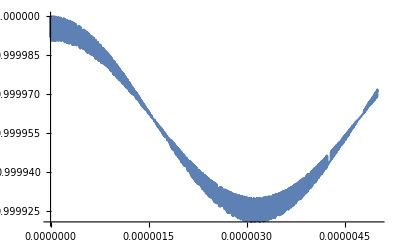

Initial angular momentum: 0

Average probability: 1.

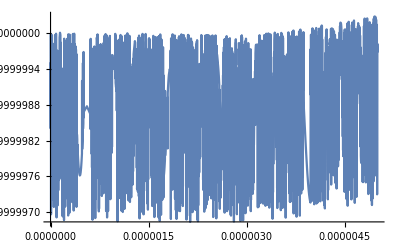

Initial angular momentum: 0

Average probability: 1.

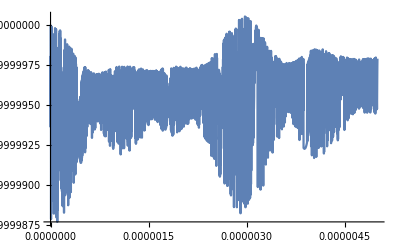

Initial angular momentum: 1

Average probability: 0.999953

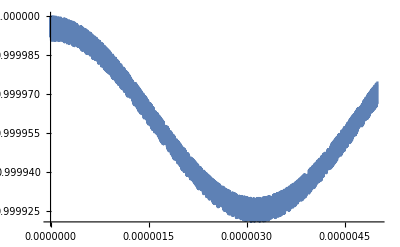

Initial angular momentum: 1

Average probability: 0.999954

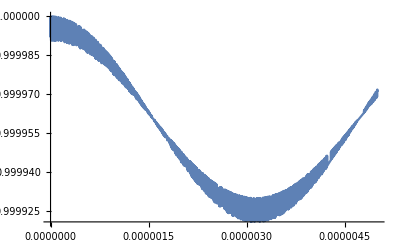

Initial angular momentum: 2

Average probability: 1.

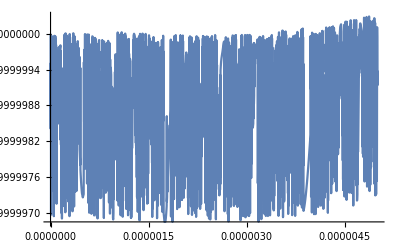

```mathematica
For[i=1,i≤Length[puresStateAngularMomenta],i++,

density0 = pureStateDensityMatrices[[i]];
pureStates =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten;
params = { diffeqs, pureStates } // Flatten;

sol = NDSolve[ params /. f -> pulseFreq, funcs, {t, tStart, tEnd}, 
PrecisionGoal->10,AccuracyGoal->10, MaxSteps->Infinity];

densitySol = density /. sol[[1]];

basisStates = getBasisStatesWithAngularMomentum[ puresStateAngularMomenta[[i]]];
angMomFuncs = Map[ Conjugate[#] .  densitySol. # &, basisStates];

avgProb = 1/(tEnd - tStart)NIntegrate[ angMomFuncs . angMomFuncs, {t, tStart, tEnd}];

Print[ "Initial angular momentum: ",  puresStateAngularMomenta[[i]]] ;
Print[ "Average probability: ",  avgProb] ;

Print[Plot[ angMomFuncs . angMomFuncs, {t, tStart, tEnd}]];
 ]
```